```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210628_finalising/fxd_coefficients"];
```

```mathematica
Get["../../algoritm_packages/SingleNetworks-algorithm-package-2.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
stoichioforhomosapiens=Drop[Import["../../210324_disc_time_windows_and_OR_model/iAT_PLT_636_stoichiomat.csv",HeaderLines->1],None,{1}];
SparseArray@stoichioforhomosapiens
```

SparseArray[…]

```mathematica
stoichiometricmatrix=stoichioforhomosapiens;
metabolites=738;
fluxexchanges=1008;
steadystatevector=ConstantArray[{0,0},metabolites];
first[a_]:=First/@GatherBy[Ordering@a,a[[#]]&]//Sort;
```

```mathematica
case="coeffs";
interval="(-1,1)";
val="5";
val2="quadrupled";

objfunctions=Import["C:/Users/serha/NonDrive/OR_model-25.06.2021/objective_functions/"<>interval<>"objfunc_fxd"<>case<>".mx"];
boundaries=Import["../cases/boundaries_for_deleted_reaction_series_-5and5_"<>val2<>".mx"];
subsetpositionsforsequences=Import["../cases/subsetpositionsforsequences.mx"];
boundariespos0=Table[Position[boundaries[[i]],{0,0}],{i,10}];
boundariesposval=Table[Position[boundaries[[i]],{-5,5}],{i,10}];
boundariesa=Table[ReplacePart[(Table[ReplacePart[ConstantArray[{-500,500},fluxexchanges],MapThread[#1->#2&,{boundariespos0[[i]],ConstantArray[{0,0},Length@boundariespos0[[i]]]}]],{i,10}])[[j]],MapThread[#1->#2&,{boundariesposval[[j]],ConstantArray[{-ToExpression@val,ToExpression@val},Length@boundariesposval[[j]]]}]],{j,10}];
```

```mathematica
AbsoluteTiming[resultset=Table[Table[Chop[Table[Quiet@LinearProgramming[-objfunctions[[j,i]],stoichiometricmatrix,steadystatevector,k],{i,50}],10^-5],{j,Length@objfunctions}],{k,boundariesa}];]
```

LinearProgramming::lpipncv: The interior point algorithm cannot converge to the tolerance of 1.49012×10^-8. The best residual achieved is 0.000189937. The failure to converge might be because the problem is mildly infeasible. Setting the option Method -> RevisedSimplex should give a more definite answer, though large problems may take longer computing time.

LinearProgramming::lpipncv: The interior point algorithm cannot converge to the tolerance of 1.49012×10^-8. The best residual achieved is 0.000476796. The failure to converge might be because the problem is mildly infeasible. Setting the option Method -> RevisedSimplex should give a more definite answer, though large problems may take longer computing time.

{5314.6,Null}

```mathematica
Export["C:/Users/serha/NonDrive/OR_model-25.06.2021/solution_vectors/"<>interval<>"solutionvectors_fxd"<>case<>"_-"<>val<>"and"<>val<>"_"<>val2<>"pcs.mx",Table[Flatten[resultset[[i]],1],{i,10}]]
```

C:/Users/serha/NonDrive/OR_model-25.06.2021/solution_vectors/(-1,1)solutionvectors_fxdcoeffs_-5and5_quadrupledpcs.mx

```mathematica
solutionvectorslist=Import["C:/Users/serha/NonDrive/OR_model-25.06.2021/solution_vectors/"<>interval<>"solutionvectors_fxd"<>case<>"_-"<>val<>"and"<>val<>"_"<>val2<>"pcs.mx"];
(*solutionvectorslist=Table[Flatten[resultset[[i]],1],{i,10}];*)
```

LinearProgramming::lpipncv: The interior point algorithm cannot converge to the tolerance of 1.49012×10^-8. The best residual achieved is 0.000189937. The failure to converge might be because the problem is mildly infeasible. Setting the option Method -> RevisedSimplex should give a more definite answer, though large problems may take longer computing time.

LinearProgramming::lpipncv: The interior point algorithm cannot converge to the tolerance of 1.49012×10^-8. The best residual achieved is 0.000476796. The failure to converge might be because the problem is mildly infeasible. Setting the option Method -> RevisedSimplex should give a more definite answer, though large problems may take longer computing time.

```mathematica
objfunctionslist=Table[Flatten[objfunctions,1],{i,10}];
```

```mathematica
AbsoluteTiming[featuredatalist=Table[MapThread[Dot,{objfunctionslist[[j]],solutionvectorslist[[j]]}],{j,10}];]
```

{2.37461,Null}

LinearProgramming::lpipncv: The interior point algorithm cannot converge to the tolerance of 1.49012×10^-8. The best residual achieved is 0.000189937. The failure to converge might be because the problem is mildly infeasible. Setting the option Method -> RevisedSimplex should give a more definite answer, though large problems may take longer computing time.

LinearProgramming::lpipncv: The interior point algorithm cannot converge to the tolerance of 1.49012×10^-8. The best residual achieved is 0.000476796. The failure to converge might be because the problem is mildly infeasible. Setting the option Method -> RevisedSimplex should give a more definite answer, though large problems may take longer computing time.

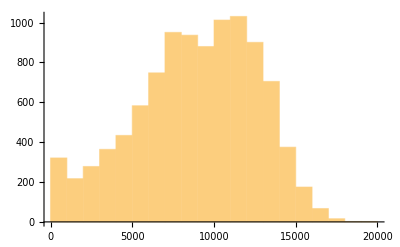
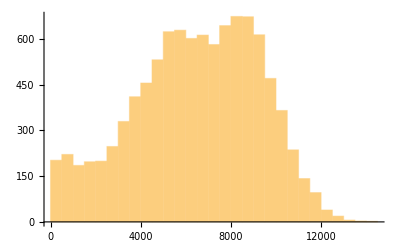
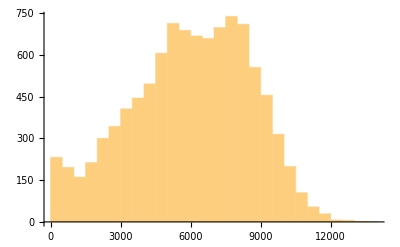
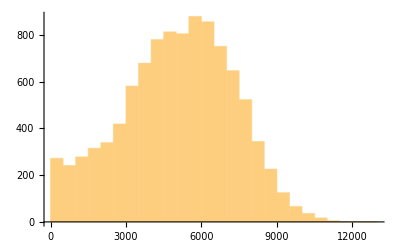
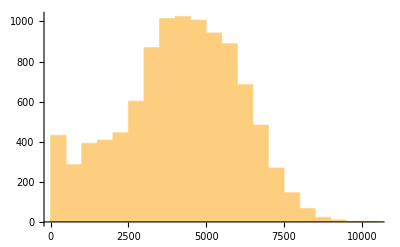
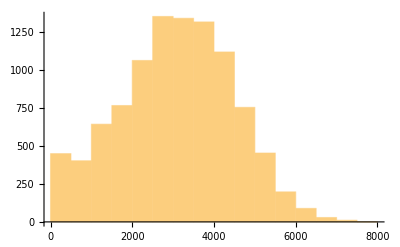
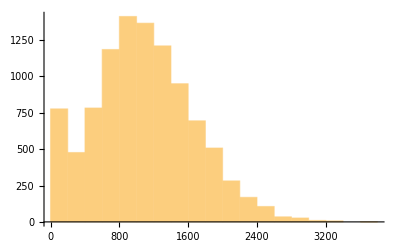
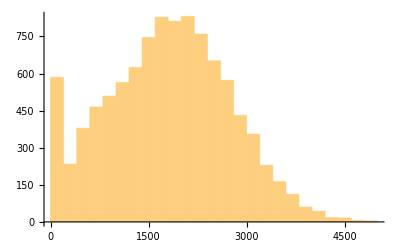

```mathematica
datafulllist=Table[Join[Partition[Range@10000,1],Partition[Flatten@Table[ConstantArray[i,50],{i,200}],1],Partition[featuredatalist[[j]],1],2],{j,10}];
Table[Histogram@datafulllist[[i]][[All,3]],{i,10}]
```

```mathematica
thread={{1,450},{2,330},{3,320},{4,310},{5,240},{6,170},{7,70},{8,110},{9,100},{10,100}};
Mean@thread[[All,2]]
```

220

```mathematica
thread=Thread[{Range@10,780}]
```

{{1,780},{2,780},{3,780},{4,780},{5,780},{6,780},{7,780},{8,780},{9,780},{10,780}}

```mathematica
AbsoluteTiming[widthdataFixedstep2=Table[snetworkdatabinned[3,i[[2]],datafulllist[[i[[1]]]]],{i,thread}];]
```

{344.899,Null}

```mathematica
graphsandnodenumbers12=Table[snetworkgraph[widthdataFixedstep2[[i]][[1]],widthdataFixedstep2[[i]][[2]],2,7,400,Green],{i,10}];
graphsandnodenumbers12[[All,2]]
```

{25,19,18,17,14,10,5,7,6,6}

```mathematica
modularityvalues12=Table[N@GraphAssortativity[graphsandnodenumbers12[[i]][[1]],FindGraphCommunities[graphsandnodenumbers12[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers12}];
```

```mathematica
singlerandomgraphsdegfxd12=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers12[[All,1]]}];
singlerandomerdrenmodularityvalues12=Table[N@GraphAssortativity[singlerandomgraphsdegfxd12[[i]],FindGraphCommunities[singlerandomgraphsdegfxd12[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd12}];
singlerandomgraphscomm12=Table[randomizinggraphmod[i],{i,graphsandnodenumbers12[[All,1]]}];
singlerandomcommmodularityvalues12=Table[N@GraphAssortativity[singlerandomgraphscomm12[[i]],FindGraphCommunities[singlerandomgraphscomm12[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm12}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity12=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers12[[All,1]]}];]
```

Power::infy: Infinite expression 1/0. encountered.

{104.516,Null}

```mathematica
bucketnode12=graphsandnodenumbers12[[All,2]]
```

{25,19,18,17,14,10,5,7,6,6}

Min::nord: Invalid comparison with ComplexInfinity attempted.

Max::nord: Invalid comparison with ComplexInfinity attempted.

ListLinePlot::prng: Value of option PlotRange -> {{0,11},{-1+Min[-0.988425,ComplexInfinity],1+Max[8.88798,ComplexInfinity]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

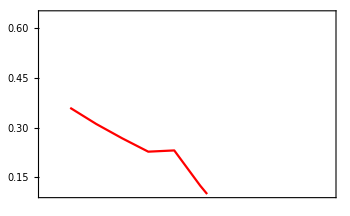
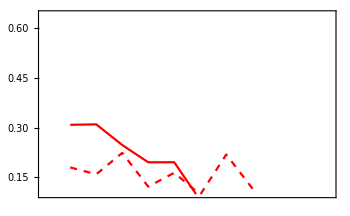
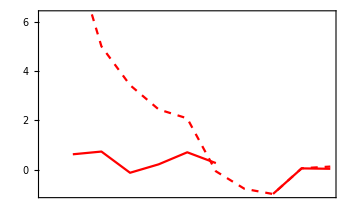

```mathematica
modularityvaluestimewinsmall=modularityvalues12;
randommodtimewinsmalldegreefxd=singlerandomerdrenmodularityvalues12;
randommodtimewinsmallcomm=singlerandomcommmodularityvalues12;
Zscoretimewinsmall=Zscoresmodularity12;
modularityplotrange={0.1,0.64};
(*MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,singlerandomerdrenmodularityvalues1,modularityvalues12}]*)
padding=38;
win2=10;
Row[{ListLinePlot[Thread[{Range@win2,modularityvaluestimewinsmall}],Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0,win2+1},modularityplotrange}],
Row[{ListLinePlot[{Thread[{Range@win2,randommodtimewinsmalldegreefxd}],Thread[{Range@win2,randommodtimewinsmallcomm}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{0,win2+1},modularityplotrange}],
ListLinePlot[{Thread[{Range@win2,Zscoretimewinsmall[[All,1]]}],Thread[{Range@win2,Zscoretimewinsmall[[All,2]]}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{0,win2+1},MinMax[Flatten[Zscoretimewinsmall],1]}]}],LineLegend[{Dashed,Black},{"Degrees Fixed N.M.","Modularity N.M."},LegendMargins->0,LegendMarkerSize->{20,20}],Spacer@0.1}]
```

```mathematica
AbsoluteTiming[widthdataFixedbucket2=Table[snetworkdatafxdbucket[3,bucketnode12[[i]],datafulllist[[i]]],{i,10}];]
```

{414.724,Null}

```mathematica
graphsandnodenumbers32=Table[snetworkgraph[widthdataFixedbucket2[[i]][[1]],widthdataFixedbucket2[[i]][[2]],1.5,7,400,Green],{i,10}];
modularityvalues32=Table[N@GraphAssortativity[graphsandnodenumbers32[[i]][[1]],FindGraphCommunities[graphsandnodenumbers32[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers32}];
```

```mathematica
singlerandomgraphsdegfxd32=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers32[[All,1]]}];
singlerandomerdrenmodularityvalues32=Table[N@GraphAssortativity[singlerandomgraphsdegfxd32[[i]],FindGraphCommunities[singlerandomgraphsdegfxd32[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd32}];
singlerandomgraphscomm32=Table[randomizinggraphmod[i],{i,graphsandnodenumbers32[[All,1]]}];
singlerandomcommmodularityvalues32=Table[N@GraphAssortativity[singlerandomgraphscomm32[[i]],FindGraphCommunities[singlerandomgraphscomm32[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm32}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity32=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers32[[All,1]]}];]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{42.2979,Null}

ListLinePlot::prng: Value of option PlotRange -> {{0,11},{Indeterminate,Indeterminate}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

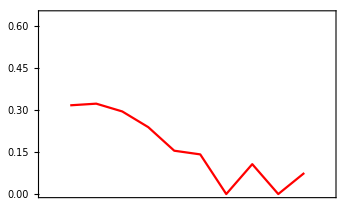
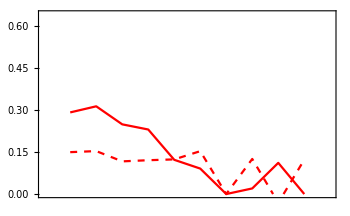
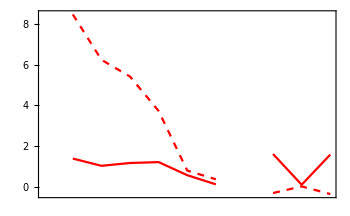

```mathematica
modularityvaluestimewinsmall=modularityvalues32;
randommodtimewinsmalldegreefxd=singlerandomerdrenmodularityvalues32;
randommodtimewinsmallcomm=singlerandomcommmodularityvalues32;
Zscoretimewinsmall=Zscoresmodularity32;
modularityplotrange={0,0.64};
(*MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,singlerandomerdrenmodularityvalues1,modularityvalues12}]*)
padding=38;
win2=10;
Row[{ListLinePlot[Thread[{Range@win2,modularityvaluestimewinsmall}],Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0,win2+1},modularityplotrange}],
Row[{ListLinePlot[{Thread[{Range@win2,randommodtimewinsmalldegreefxd}],Thread[{Range@win2,randommodtimewinsmallcomm}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{0,win2+1},modularityplotrange}],
ListLinePlot[{Thread[{Range@win2,Zscoretimewinsmall[[All,1]]}],Thread[{Range@win2,Zscoretimewinsmall[[All,2]]}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{0,win2+1},MinMax[Flatten[Zscoretimewinsmall],1]}]}],LineLegend[{Dashed,Black},{"Degrees Fixed N.M.","Modularity N.M."},LegendMargins->0,LegendMarkerSize->{20,20}],Spacer@0.1}]
```

```mathematica
Export["plot_values/fxd_"<>case<>"/-"<>val<>"+"<>val<>"_"<>val2<>"_"<>interval<>"-modularityvalues-fss.mx",modularityvalues12]
Export["plot_values/fxd_"<>case<>"/-"<>val<>"+"<>val<>"_"<>val2<>"_"<>interval<>"-singrand-erd-modularityvalues-fss.mx",singlerandomerdrenmodularityvalues12]
Export["plot_values/fxd_"<>case<>"/-"<>val<>"+"<>val<>"_"<>val2<>"_"<>interval<>"-singrand-comm-modularityvalues-fss.mx",singlerandomcommmodularityvalues12]
Export["plot_values/fxd_"<>case<>"/-"<>val<>"+"<>val<>"_"<>val2<>"_"<>interval<>"-zscores-fss.mx",Zscoresmodularity12]
Export["plot_values/fxd_"<>case<>"/-"<>val<>"+"<>val<>"_"<>val2<>"_"<>interval<>"-modularityvalues-fbs.mx",modularityvalues32]
Export["plot_values/fxd_"<>case<>"/-"<>val<>"+"<>val<>"_"<>val2<>"_"<>interval<>"-singrand-erd-modularityvalues-fbs.mx",singlerandomerdrenmodularityvalues32]
Export["plot_values/fxd_"<>case<>"/-"<>val<>"+"<>val<>"_"<>val2<>"_"<>interval<>"-singrand-comm-modularityvalues-fbs.mx",singlerandomcommmodularityvalues32]
Export["plot_values/fxd_"<>case<>"/-"<>val<>"+"<>val<>"_"<>val2<>"_"<>interval<>"-zscores-fbs.mx",Zscoresmodularity32]
```

plot_values/fxd_coeffs/-5+5_quadrupled_(-1,1)-modularityvalues-fss.mx

plot_values/fxd_coeffs/-5+5_quadrupled_(-1,1)-singrand-erd-modularityvalues-fss.mx

plot_values/fxd_coeffs/-5+5_quadrupled_(-1,1)-singrand-comm-modularityvalues-fss.mx

plot_values/fxd_coeffs/-5+5_quadrupled_(-1,1)-zscores-fss.mx

plot_values/fxd_coeffs/-5+5_quadrupled_(-1,1)-modularityvalues-fbs.mx

plot_values/fxd_coeffs/-5+5_quadrupled_(-1,1)-singrand-erd-modularityvalues-fbs.mx

plot_values/fxd_coeffs/-5+5_quadrupled_(-1,1)-singrand-comm-modularityvalues-fbs.mx

plot_values/fxd_coeffs/-5+5_quadrupled_(-1,1)-zscores-fbs.mx